```mathematica
T[x_]:=Piecewise[{{2 x + 1/2, 0 ≤ x < 1/4},{-x+5/4,1/4≤x<1/2},{-2 x + 7/4, 1/2≤x<3/4},{-x+1,3/4≤ x ≤ 1}}]
```

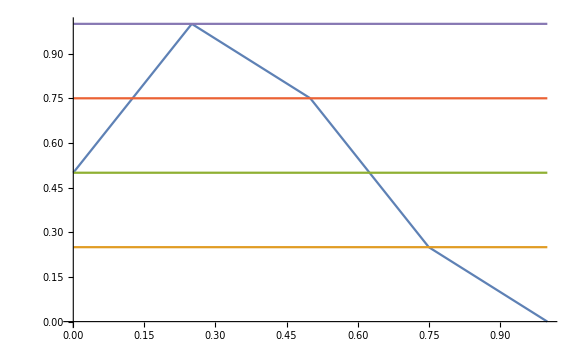

```mathematica
Plot[{T[x],1/4,1/2,3/4,1},{x,0,1}]
```

```mathematica
M:={{0,0,1/2,1},{0,0,0,1},{0,1/2,1,0},{1/2,0,0,0}}
```

```mathematica
MatrixForm[M]
```

(0 | 0 | 1/2 | 1
0 | 0 | 0 | 1
0 | 1/2 | 1 | 0
1/2 | 0 | 0 | 0)

```mathematica
Eigensystem[M]
```

{{1/2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,2],1/2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,1],1/2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,4],1/2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,3]},{{1/2 (4-2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,2]-2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,2]^2+Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,2]^3),1/2 (-4+3 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,2]+2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,2]^2-Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,2]^3),1/2 (-2+Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,2]^2),1},{1/2 (4-2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,1]-2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,1]^2+Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,1]^3),1/2 (-4+3 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,1]+2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,1]^2-Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,1]^3),1/2 (-2+Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,1]^2),1},{1/2 (4-2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,4]-2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,4]^2+Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,4]^3),1/2 (-4+3 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,4]+2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,4]^2-Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,4]^3),1/2 (-2+Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,4]^2),1},{1/2 (4-2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,3]-2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,3]^2+Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,3]^3),1/2 (-4+3 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,3]+2 Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,3]^2-Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,3]^3),1/2 (-2+Root[-2+4 #1-2 #1^2-2 #1^3+#1^4&,3]^2),1}}}